ResourceFunction["MaTeXInstall"][]

```mathematica
<<MaTeX`
```

```mathematica
TempArray={0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085}
```

{0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085}

```mathematica
Tc=0.082
```

0.082

```mathematica
AvgCurvatureA ={11.95,11.97,12.03,12.15,12.28,12.4,12.49,12.53,12.56,12.55,12.53,12.5,12.44,12.33,12.2,12.07};
```

```mathematica
AvgCurvatureB={13.77,13.74,13.67,13.6,13.51,13.4,13.27,13.15,13.02,12.88,12.74,12.61,12.47,12.33,12.2,12.07};
```

```mathematica
betaArray = 1/TempArray;
```

```mathematica
curvxxGS=Table[1/AvgCurvatureA[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{0.083682,0.0835422,0.0831255,0.0823045,0.0814332,0.0806452,0.0800641,0.0798085,0.0796178,0.0796813,0.0798085,0.08,0.0803859,0.081103,0.0819672,0.08285}

```mathematica
curvxxES=Table[1/AvgCurvatureB[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{0.0726216,0.0727802,0.0731529,0.0735294,0.0740192,0.0746269,0.075358,0.0760456,0.0768049,0.0776398,0.0784929,0.0793021,0.0801925,0.081103,0.0819672,0.08285}

```mathematica
TBG=Tc*0.8
```

0.0656

```mathematica
w0=1;
```

```mathematica
wTBG=0.1;
```

```mathematica
scattRateArray = Table[w0+wTBG (Sqrt[Sqrt[1+(TempArray[[n]]/TBG)^4]]-1),{n,1,Dimensions[TempArray][[1]]}]
```

{1.00001,1.00007,1.00022,1.00052,1.00108,1.00197,1.00329,1.00513,1.00754,1.01056,1.01418,1.01838,1.0231,1.02829,1.03387,1.03979}

```mathematica
ρxx=curvxxGS*scattRateArray
```

{0.0836831,0.0835479,0.0831434,0.0823476,0.0815208,0.0808038,0.0803275,0.0802177,0.0802182,0.0805227,0.0809404,0.0814704,0.082243,0.0833972,0.0847435,0.0861468}

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->40};
```

```mathematica
legend=SwatchLegend[{Blue,Orange},{MaTeX["\\text{Ordered}",Magnification->2.5],MaTeX["\\text{Disordered}",Magnification->2.5]},LegendMarkers->Graphics[{EdgeForm[Black],Disk[]}],LegendMarkerSize->{16,16}];
```

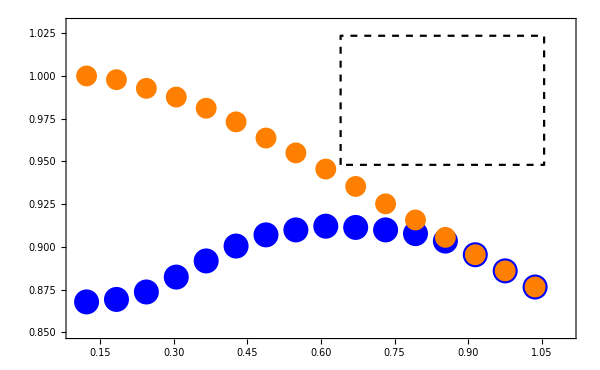

```mathematica
Legended[Show[ListPlot[Transpose@{TempArray/Tc,AvgCurvatureA/Max[AvgCurvatureB]},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0.1,1.1},{0.85,1.03}}],ListPlot[Transpose@{TempArray/Tc,AvgCurvatureB/Max[AvgCurvatureB]},PlotStyle->{Orange,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[{{0.64,0.948},{0.64,1.0235},{1.055,1.0235},{1.055,0.948},{0.64,0.948}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->3],MaTeX["C(T)",Magnification->3]},
BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->600],Placed[legend,Scaled[{0.75,0.75}]]]
```

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
```

```mathematica
Min[ρxx]
```

0.0802177

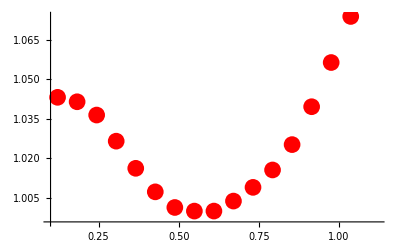

```mathematica
p1=ListPlot[Transpose@{TempArray/Tc,ρxx/Min[ρxx]},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0.1,1.12},All}]
```

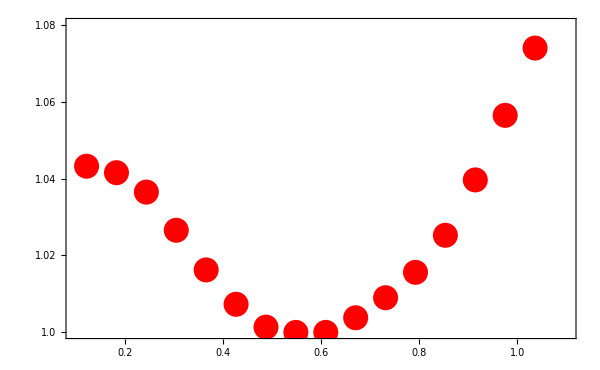

```mathematica
Show[p1,FrameTicks-> {{{{1.0,"1.0"},1.02,1.04,1.06,1.08},None},{{{0.2,"0.2"},{0.4,"0.4"},{0.6,"0.6"},{0.8,"0.8"},{1.0,"1.0"},{1.2,"1.2"}},None}},Frame->True,
PlotRange->{{0.1,1.1},{1.0,1.08}},FrameLabel->{MaTeX["T/T_c",Magnification->3],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{min}}",Magnification->3.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600]
```